## Animate a Guass Gun

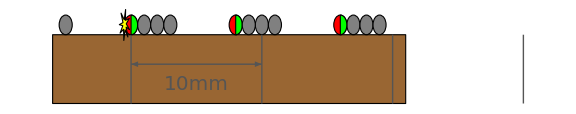

```mathematica
r = 0.005;(*radius of ball in m*)
a = 8; (*units of r*)
n=3;(*units of 2r*)
Nmag = 3;
(*
 (2r)   a     (2r)(2r)(2r)  a     (2r)(2r)(2r)
    a    (2r)(2r)(2r)  a     (2r)(2r)(2r)(2r)
*)
DrawMagnet[x_,r_]:= {Red,Disk[{x,0},r] ,Green, Disk[{x,0},r,{-π/2,π/2}]  }
DrawBall[x_,r_]:= {Gray,Disk[{x,0},r]  };

DrawCollision[x_,r_]:={Yellow,Module[{kmax = 16},

Polygon[Table[θ =2(π k)/kmax+RandomReal[(2π)/kmax]; {x,0}+r.8{Sin[θ],2Cos[θ]}If[EvenQ[k],1,1/3],{k,1,kmax}]]
]};

Graphics[{EdgeForm[Black],
Brown, Rectangle[{-(4+a)r,-8r}, {Nmag( a+ 2n)r,-r}],
DrawBall[-(2+a)r,r],

 ,Table[ {DrawMagnet[stages 2(a/2+1+n)r,r],Table[DrawBall[stages 2(a/2+1+n)r+balls 2r,r],{balls,1,n}]},{stages,0,Nmag-1}],DrawCollision[-r,r]

(*draw trajectory!   Fgrav = -9.81*mass*)


(*draw scale bar*)
,Darker[Gray],Table[Line[{{x/10,-8r},{x/10,-r}}],{x,0,Floor[Nmag( a+ 2n)r*10+1]}]
,Arrowheads[{-.03,.03}],Arrow[{{0,-4r},{1/10,-4r}}],Text[Style["10mm",20],{1/20,-6r}]

},ImageSize-> Large]
```

TODO:
Add a manipulation slider with 5 stages for each moving ball (Nmag+1), and an animation step for each intermediate collision (a+1)*Nmag

Assume that the steel ball - bearings have negligible effect on magnetic field (not true)
Assume no rolling resistance
No ohmic heating, Elastic collisions.

```mathematica
"
```

```mathematica
interSteps = 4;
Manipulate[Module[{magpos,ofset,ballpos},
If[ a<2(n-1),a=2(n-1)]; (*if a<2(n-1), the starting configuration is not stable*)
Graphics[{
(*background*)
White, Rectangle[{-(4+a)r,0},{(Nmag) 2(a/2+1+n)r-(1+a) r+0.1,2r}],
(*Floor*)
EdgeForm[Black],
Brown, Rectangle[{-(4+a)r,-8r}, {(Nmag)2(a/2+1+n)r-(1+a)r,-r}],
(*Initial ball*)
DrawBall[-(2+a)r +a r Min[(aStep/interSteps)^1,1],r],

 ,(*rest of balls and magnets*)Table[
magpos = stages 2(a/2+1+n)r;
 {DrawMagnet[magpos,r],
Table[DrawBall[magpos+balls 2r,r],{balls,1,n-1}],
(*make the ball advance if needed       *)
ballpos=magpos+n 2r+a r Max[0, Min[((aStep-(stages+1)( interSteps+n+1)+1)/(interSteps+1))^1,1]];
,DrawBall[ballpos,r]
},{stages,0,Nmag-1}],

(*Draw Collisions*)
 If[ ofset = Mod[ aStep,(interSteps+n+1)]-interSteps ; ofset ≥ 0 && aStep<Nmag(interSteps+n+1),
{DrawCollision[(2ofset-1 +2( a/2+1+n) Floor[aStep/(interSteps+n+1)])r,r]
,(*annotate velocity if collision*)
Black,Text[Style["Xm/s",20],{(2ofset +2( a/2+1+n)  Floor[aStep/(interSteps+n+1)])r,2r}]},
{(*annotate velocity if no collision*)
Black,Text[Style["Xm/s",20],{((a ofset)/(interSteps+1) -2+2( a/2+1+n) Floor[aStep/(interSteps+n+1)])r,2r}]}
]


(*draw trajectory!   Fgrav = -9.81*mass*)

(*draw scale bar and ticks*)
,Darker[Gray],Table[Line[{{x/10,-8r},{x/10,-r}}],{x,0,Floor[((Nmag)2(a/2+1+n)r-(1+a)r)*10+1]}]
,Arrowheads[{-.03,.03}],Arrow[{{0,-4r},{1/10,-4r}}],Text[Style["10mm",20],{1/20,-6r}]

},ImageSize-> Large] ]

,
{{r,0.005,"ball radius (m)"},0.0005,0.01,Appearance->"Labeled"},
{{a,8,"air gap (ball radii)"},1,20,Appearance->"Labeled"},
{{Nmag,2,"stages"},1,10,1,Appearance->"Labeled"},
{{n,3,"balls per stage"},2,10,1,Appearance->"Labeled"},
{{aStep,0,"Animate"},0,interSteps(Nmag+1)+(n+1)Nmag,1,AnimationDirection->Forward,Appearance->"Open"},AppearanceElements->"Open"]
```